## Parameters

```mathematica
m = 0.973; (*Kg*)
g = 9.81;
Iz =0.0016155926; (*Kg m^2*) 
rl1[l1_, ϕ1_]:=l1*{Cos[ϕ1],-Sin[ϕ1]};
rl2[l2_, ϕ2_]:=l2*{-Cos[ϕ2],-Sin[ϕ2]};
r1 = {-0.0847,0.0525};
r2 = {0.084,0.0525};
rp = {0,0.053086};
W = 1.3780;
H = 1.372;
w = 0.1694;
```

## Kinematics

```mathematica
KineChainEQ =rl1[l1[t], ϕ1[t]]+RotationMatrix[α[t]].(-r1)-({W,0}+rl2[l2[t], ϕ2[t]]+RotationMatrix[α[t]].(-r2))=={0,0};
KineChainEQList = Thread@KineChainEQ
```

{-1.378+0.1687 Cos[α[t]]+Cos[ϕ1[t]] l1[t]+Cos[ϕ2[t]] l2[t]==0,0.+0.1687 Sin[α[t]]-l1[t] Sin[ϕ1[t]]+l2[t] Sin[ϕ2[t]]==0}

```mathematica
KineConstraints = {l1[t]>0, l2[t]>0, -π/2<α[t]<π/2, 0<ϕ1[t]<π/2, 0<ϕ2[t]<π/2};
KineChainEQReduced = Assuming[KineConstraints, Eliminate[KineChainEQList, ϕ2[t]]]//Simplify;
FConstraint = KineChainEQReduced[[1]]-KineChainEQReduced[[2]]
```

Eliminate::ifun: Inverse functions are being used by Eliminate, so some solutions may not be found; use Reduce for complete solution information.

5.71234-1.378 Cos[α[t]]+2.96384 l1[t]^2-2.96384 l2[t]^2+l1[t] ((-8.16835+1. Cos[α[t]]) Cos[ϕ1[t]]-1. Sin[α[t]] Sin[ϕ1[t]])

```mathematica
r = rl1[l1[t], ϕ1[t]]+RotationMatrix[α[t]].(-r1)
```

{0.0847 Cos[α[t]]+Cos[ϕ1[t]] l1[t]+0.0525 Sin[α[t]],-0.0525 Cos[α[t]]+0.0847 Sin[α[t]]-l1[t] Sin[ϕ1[t]]}

## Kinetic Energy (T)

```mathematica
v= Sqrt[D[r[[1]],t]^2+D[r[[2]],t]^2];
ω = D[α[t],t];
T= 1/2 m v^2 +1/2 Iz ω^2
```

0.000807796 α'[t]^2+0.4865 ((-Sin[ϕ1[t]] l1'[t]+0.0847 Cos[α[t]] α'[t]+0.0525 Sin[α[t]] α'[t]-Cos[ϕ1[t]] l1[t] ϕ1'[t])^2+(Cos[ϕ1[t]] l1'[t]+0.0525 Cos[α[t]] α'[t]-0.0847 Sin[α[t]] α'[t]-l1[t] Sin[ϕ1[t]] ϕ1'[t])^2)

## Potential Energy (U)

```mathematica
U= m*g*r[[2]]
```

9.54513 (-0.0525 Cos[α[t]]+0.0847 Sin[α[t]]-l1[t] Sin[ϕ1[t]])

## Lagrange Equations

```mathematica
L= T-U
```

-9.54513 (-0.0525 Cos[α[t]]+0.0847 Sin[α[t]]-l1[t] Sin[ϕ1[t]])+0.000807796 α'[t]^2+0.4865 ((-Sin[ϕ1[t]] l1'[t]+0.0847 Cos[α[t]] α'[t]+0.0525 Sin[α[t]] α'[t]-Cos[ϕ1[t]] l1[t] ϕ1'[t])^2+(Cos[ϕ1[t]] l1'[t]+0.0525 Cos[α[t]] α'[t]-0.0847 Sin[α[t]] α'[t]-l1[t] Sin[ϕ1[t]] ϕ1'[t])^2)

```mathematica
LEQ[q_] := D[D[L,q'[t]],t]-D[L,q[t]]-λ[t]*D[FConstraint, q[t]]==0
```

```mathematica
allLEQ = LEQ/@{ϕ1,α}//Simplify;
```

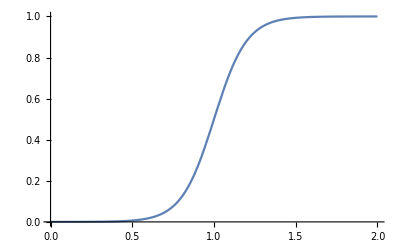

```mathematica
Plot[(1+Tanh[(x-1) 5])/2,{x,0,2}]
```

```mathematica
l1prime[t_] :=1+(1/4)*((1+Tanh[(t-1) 5])/2);
l2prime[t_] := 1;
initC = {α[0]==0 Degree, α'[0]==0};
```

```mathematica
Join[{FConstraint==0},allLEQ, initC]
```

{5.71234-1.378 Cos[α[t]]+2.96384 l1[t]^2-2.96384 l2[t]^2+l1[t] ((-8.16835+1. Cos[α[t]]) Cos[ϕ1[t]]-1. Sin[α[t]] Sin[ϕ1[t]])==0,l1[t] (-9.81 Cos[ϕ1[t]]+(-8.39501 Sin[ϕ1[t]]+1.02775 Sin[α[t]+ϕ1[t]]) λ[t]+(-0.0525 Cos[α[t]+ϕ1[t]]+0.0847 Sin[α[t]+ϕ1[t]]) α'[t]^2+2. l1'[t] ϕ1'[t]-0.0847 Cos[α[t]+ϕ1[t]] α''[t]-0.0525 Sin[α[t]+ϕ1[t]] α''[t]+1. l1[t] ϕ1''[t])==0,1. Cos[α[t]]+0.619835 Sin[α[t]]+(-1.70445 Sin[α[t]]+1.2369 l1[t] Sin[α[t]+ϕ1[t]]) λ[t]+(-0.203874 Cos[α[t]+ϕ1[t]]-0.126368 Sin[α[t]+ϕ1[t]]) l1'[t] ϕ1'[t]+0.101937 l1[t] Sin[α[t]+ϕ1[t]] ϕ1'[t]^2+0.063184 Cos[α[t]+ϕ1[t]] l1''[t]+0.0139495 α''[t]==0.063184 Cos[α[t]+ϕ1[t]] l1[t] ϕ1'[t]^2+0.101937 Sin[α[t]+ϕ1[t]] l1''[t]+0.101937 Cos[α[t]+ϕ1[t]] l1[t] ϕ1''[t]+0.063184 l1[t] Sin[α[t]+ϕ1[t]] ϕ1''[t],α[0]==0,α'[0]==0}

```mathematica
NDSol[{l1prime_, l2prime_}, initc_, {t1_, t2_}]:= Module[{},
NDSolve[Join[{FConstraint==0},allLEQ, initC]/.{l1->l1prime, l2->l2prime},{α,ϕ1,λ},{t,t1,t2}, Method->{"IndexReduction"->Automatic}]
];
```

```mathematica
sol = NDSol[{l1prime, l2prime},initC, {0,5}]
```

{{α→InterpolatingFunction[…],ϕ1→InterpolatingFunction[…],λ→InterpolatingFunction[…]}}

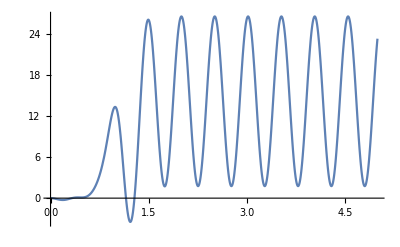

```mathematica
Plot[180/π*α[t]/.sol, {t,0,5}]
```

## Animate :)

```mathematica
rFunc[tt_]:=r/.t->tt/.First@sol
```

```mathematica
BotAnimation[sol_, {t1_,t2_}]:=
Module[{points,penpoint, αprime, ϕ1prime, botFrame, botFrameList},
αprime[t_]=α[t]/.First@sol;
ϕ1prime[t_]=ϕ1[t]/.First@sol;
points[t_] := Join[{{0,0}},Accumulate[{rl1[l1prime[t], ϕ1prime[t]],RotationMatrix[αprime[t]].(-r1),RotationMatrix[αprime[t]].(r2)}], {{W,0}}];
penpoint[t_]:=points[t][[3]]+ RotationMatrix[αprime[t]].rp;
botFrame[t_]:=Show[{Graphics[{Gray,Line[points[t][[{1,2,4,5}]]], Thick,Red, Line[points[t][[2;;4]]], Line[{points[t][[3]], penpoint[t]}]}],
If[t>t1,ParametricPlot[penpoint[tp],{tp,t1,t}],{}]}];
botFrameList = Table[botFrame[t],{t,t1,t2,1/24}];

<|"FrameList" ->botFrameList, "FrameFunc"->Function[t,botFrame[t]]|>]
```

```mathematica
BotAnimation[{l1prime_, l2prime_}, initC_, {t1_,t2_}]:=
With[{sol = NDSol[{l1prime, l2prime},initC, {t1,t2}]},
Module[{points,penpoint, αprime, ϕ1prime, botFrame, botFrameList},
αprime[t_]=α[t]/.First@sol;
ϕ1prime[t_]=ϕ1[t]/.First@sol;
points[t_] := Join[{{0,0}},Accumulate[{rl1[l1prime[t], ϕ1prime[t]],RotationMatrix[αprime[t]].(-r1),RotationMatrix[αprime[t]].(r2)}], {{W,0}}];
penpoint[t_]:=points[t][[3]]+ RotationMatrix[αprime[t]].rp;
botFrame[t_]:=Show[{Graphics[{Gray,Line[points[t][[{1,2,4,5}]]], Thick,Red, Line[points[t][[2;;4]]], Line[{points[t][[3]], penpoint[t]}]}],
If[t>t1,ParametricPlot[penpoint[tp],{tp,t1,t}],{}]}];
botFrameList = Table[botFrame[t],{t,t1,t2,1/24}];

<|"FrameList" ->botFrameList, "FrameFunc"->Function[t,botFrame[t]]|>]]
```

```mathematica
animationObject = BotAnimation[{l1prime, l2prime},initC, {0,4}];
```

```mathematica
listAnim = ListAnimate[animationObject["FrameList"], AnimationRate->24]
```

## Inverse Kinetics

```mathematica
$r[t_]:={W/2, -H/2}+.5*({t,t}-.5*{1,1});
```

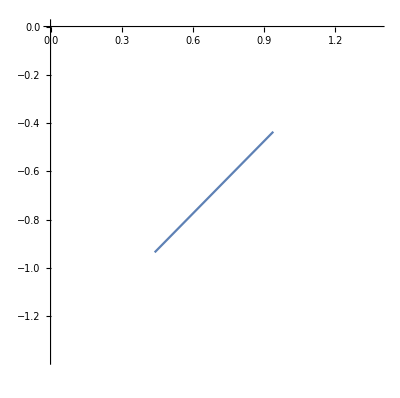

```mathematica
ParametricPlot[$r[t],{t,0,1}, PlotRange->{{0,W},{-H,0}}]
```

```mathematica
RConstraint = {$rx[t], $ry[t]}-r
```

{-0.0847 Cos[α[t]]-Cos[ϕ1[t]] l1[t]-0.0525 Sin[α[t]]+$rx[t],-1.375+t+0.0525 Cos[α[t]]-0.0847 Sin[α[t]]+l1[t] Sin[ϕ1[t]]}

```mathematica
LEQInv[q_] := D[D[L,q'[t]],t]-D[L,q[t]]-λ1[t]*D[FConstraint, q[t]]-λ2[t]*D[RConstraint[[1]], q[t]]-λ3[t]*D[RConstraint[[2]], q[t]]==0
```

```mathematica
allLEQInv = LEQInv/@{ϕ1,α,l1,l2}//Simplify;
```

```mathematica
Join[{FConstraint==0},Thread[RConstraint=={0,0}],allLEQInv]//MatrixForm
```

(5.71234-1.378 Cos[α[t]]+2.96384 l1[t]^2-2.96384 l2[t]^2+l1[t] ((-8.16835+1. Cos[α[t]]) Cos[ϕ1[t]]-1. Sin[α[t]] Sin[ϕ1[t]])==0
-0.0847 Cos[α[t]]-Cos[ϕ1[t]] l1[t]-0.0525 Sin[α[t]]+$rx[t]==0
-1.375+t+0.0525 Cos[α[t]]-0.0847 Sin[α[t]]+l1[t] Sin[ϕ1[t]]==0
l1[t] (-9.81 Cos[ϕ1[t]]+(-8.39501 Sin[ϕ1[t]]+1.02775 Sin[α[t]+ϕ1[t]]) λ1[t]-1.02775 Sin[ϕ1[t]] λ2[t]-1.02775 Cos[ϕ1[t]] λ3[t]-0.0525 Cos[α[t]+ϕ1[t]] α'[t]^2+0.0847 Sin[α[t]+ϕ1[t]] α'[t]^2+2. l1'[t] ϕ1'[t]-0.0847 Cos[α[t]+ϕ1[t]] α''[t]-0.0525 Sin[α[t]+ϕ1[t]] α''[t]+1. l1[t] ϕ1''[t])==0
15.3995 Cos[α[t]]+9.54513 Sin[α[t]]+(-26.2476 Sin[α[t]]+19.0476 l1[t] Sin[α[t]+ϕ1[t]]) λ1[t]+(1. Cos[α[t]]-1.61333 Sin[α[t]]) λ2[t]+1.61333 Cos[α[t]] λ3[t]+1. Sin[α[t]] λ3[t]+1.56977 l1[t] Sin[α[t]+ϕ1[t]] ϕ1'[t]^2+0.973 Cos[α[t]+ϕ1[t]] l1''[t]+0.214815 α''[t]==3.13955 Cos[α[t]+ϕ1[t]] l1'[t] ϕ1'[t]+1.946 Sin[α[t]+ϕ1[t]] l1'[t] ϕ1'[t]+0.973 Cos[α[t]+ϕ1[t]] l1[t] ϕ1'[t]^2+1.56977 Sin[α[t]+ϕ1[t]] l1''[t]+1.56977 Cos[α[t]+ϕ1[t]] l1[t] ϕ1''[t]+0.973 l1[t] Sin[α[t]+ϕ1[t]] ϕ1''[t]
9.54513 Sin[ϕ1[t]]+(-8.16835 Cos[ϕ1[t]]+1. Cos[α[t]+ϕ1[t]]+5.92768 l1[t]) λ1[t]+1. Sin[ϕ1[t]] λ3[t]+0.0824131 Cos[α[t]+ϕ1[t]] α'[t]^2+0.0510825 Sin[α[t]+ϕ1[t]] α'[t]^2+0.973 l1[t] ϕ1'[t]^2+0.0824131 Sin[α[t]+ϕ1[t]] α''[t]==1. Cos[ϕ1[t]] λ2[t]+0.973 l1''[t]+0.0510825 Cos[α[t]+ϕ1[t]] α''[t]
1. l2[t] λ1[t]==0)

```mathematica
NDSolInv[{rx_, ry_}, initc_, {t1_, t2_}]:= Module[{},
NDSolve[Join[{FConstraint==0},Thread[RConstraint=={0,0}],allLEQInv, initc]/.{$rx->rx, $ry->ry},{α,ϕ1,l1,l2,λ1,λ2,λ3},{t,t1,t2},  Method->{"IndexReduction"->{Automatic, "ConstraintMethod"->None}}]
];
```

```mathematica
NSolve[Join[{FConstraint==0},Thread[RConstraint=={0,0}]]/.{$rx[t]->$r[t][[1]], $ry[t]->$r[t][[2]]}/.t->0/.l2[0]->1.3, {l1[0], ϕ1[0],α[0]}]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{l1[0]→-1.08535,ϕ1[0]→-1.9288,α[0]→1.49597},{l1[0]→-0.945979,ϕ1[0]→-2.05691,α[0]→-1.04557},{l1[0]→0.945979,ϕ1[0]→1.08468,α[0]→-1.04557},{l1[0]→1.08535,ϕ1[0]→1.21279,α[0]→1.49597}}

```mathematica
initCInv ={l1[0]==0.9459790671482455,ϕ1[0]==1.0846835655663802,α[0]==-1.0455710648118974, l1'[0]==0, ϕ1'[0]==0, α'[0]==0};
```

```mathematica
solinv = NDSolInv[Map[Function[t,#]&,{W/2, -H/2}+.5*({t,t}-.5*{1,1})], initCInv, {0,1}];
```

```mathematica
solinv
```

{{α→InterpolatingFunction[…],ϕ1→InterpolatingFunction[…],l1→InterpolatingFunction[…],l2→InterpolatingFunction[…],λ1→InterpolatingFunction[…],λ2→InterpolatingFunction[…],λ3→InterpolatingFunction[…]}}

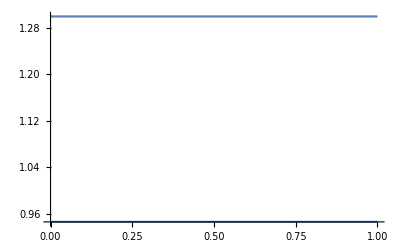

```mathematica
Plot[{l1[t],l2[t]}/.solinv, {t,0,1}]
```

## Inverse Kinetics Method 2: ry = f(rx)

```mathematica
$r[t_]:={W/2, -H/2}+.5*({t,t}-.5*{1,1});
```

```mathematica
$r[t][[1]]
```

0.689+0.5 (-0.5+t)

```mathematica
$ry[$rx_]:=$rx-.5(W+H);
```

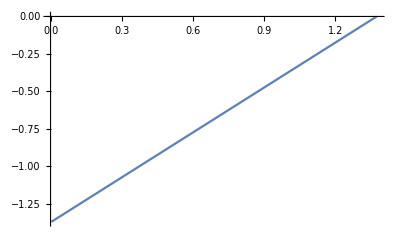

```mathematica
Plot[$ry[x],{x,0,W}, PlotRange->{{0,W},{-H,0}}]
```

```mathematica
RConstraint =r[[1]]-r[[2]]-.5*(W+H)
```

-1.375+0.1372 Cos[α[t]]+Cos[ϕ1[t]] l1[t]-0.0322 Sin[α[t]]+l1[t] Sin[ϕ1[t]]

```mathematica
LEQInv[q_] := D[D[L,q'[t]],t]-D[L,q[t]]-λ1[t]*D[FConstraint, q[t]]-λ2[t]*D[RConstraint, q[t]]==0
```

```mathematica
allLEQInv = LEQInv/@{ϕ1,α,l1,l2}//Simplify;
```

```mathematica
Join[{FConstraint==0},{RConstraint==0},allLEQInv]//MatrixForm
```

(5.71234-1.378 Cos[α[t]]+2.96384 l1[t]^2-2.96384 l2[t]^2+l1[t] ((-8.16835+1. Cos[α[t]]) Cos[ϕ1[t]]-1. Sin[α[t]] Sin[ϕ1[t]])==0
-1.375+0.1372 Cos[α[t]]+Cos[ϕ1[t]] l1[t]-0.0322 Sin[α[t]]+l1[t] Sin[ϕ1[t]]==0
l1[t] (-9.81 Cos[ϕ1[t]]+(-8.39501 Sin[ϕ1[t]]+1.02775 Sin[α[t]+ϕ1[t]]) λ1[t]+(-1.02775 Cos[ϕ1[t]]+1.02775 Sin[ϕ1[t]]) λ2[t]-0.0525 Cos[α[t]+ϕ1[t]] α'[t]^2+0.0847 Sin[α[t]+ϕ1[t]] α'[t]^2+2. l1'[t] ϕ1'[t]-0.0847 Cos[α[t]+ϕ1[t]] α''[t]-0.0525 Sin[α[t]+ϕ1[t]] α''[t]+1. l1[t] ϕ1''[t])==0
25.1078 Cos[α[t]]+15.5627 Sin[α[t]]+(-42.795 Sin[α[t]]+31.0559 l1[t] Sin[α[t]+ϕ1[t]]) λ1[t]+(1. Cos[α[t]]+4.26087 Sin[α[t]]) λ2[t]+2.55941 l1[t] Sin[α[t]+ϕ1[t]] ϕ1'[t]^2+1.58641 Cos[α[t]+ϕ1[t]] l1''[t]+0.350243 α''[t]==5.11883 Cos[α[t]+ϕ1[t]] l1'[t] ϕ1'[t]+3.17283 Sin[α[t]+ϕ1[t]] l1'[t] ϕ1'[t]+1.58641 Cos[α[t]+ϕ1[t]] l1[t] ϕ1'[t]^2+2.55941 Sin[α[t]+ϕ1[t]] l1''[t]+2.55941 Cos[α[t]+ϕ1[t]] l1[t] ϕ1''[t]+1.58641 l1[t] Sin[α[t]+ϕ1[t]] ϕ1''[t]
9.54513 Sin[ϕ1[t]]+(-8.16835 Cos[ϕ1[t]]+1. Cos[α[t]+ϕ1[t]]+5.92768 l1[t]) λ1[t]+(1. Cos[ϕ1[t]]+1. Sin[ϕ1[t]]) λ2[t]+0.0824131 Cos[α[t]+ϕ1[t]] α'[t]^2+0.0510825 Sin[α[t]+ϕ1[t]] α'[t]^2+0.973 l1[t] ϕ1'[t]^2+0.0824131 Sin[α[t]+ϕ1[t]] α''[t]==0.973 l1''[t]+0.0510825 Cos[α[t]+ϕ1[t]] α''[t]
1. l2[t] λ1[t]==0)

```mathematica
NDSolInv[initc_, {t1_, t2_}]:= Module[{},
NDSolve[Join[{FConstraint==0},{RConstraint==0},allLEQInv, initc],{α,ϕ1,l1,l2,λ1,λ2},{t,t1,t2},  Method->{"IndexReduction"->Automatic}]
];
```

```mathematica
initCInv ={l1[0]==0.9459790671482455,ϕ1[0]==1.0846835655663802,α[0]==-1.0455710648118974, l1'[0]==0, ϕ1'[0]==0, α'[0]==0};
```

```mathematica
solinv = NDSolInv[initCInv, {0,1}];
```

```mathematica
solinv
```

{{α→InterpolatingFunction[…],ϕ1→InterpolatingFunction[…],l1→InterpolatingFunction[…],l2→InterpolatingFunction[…],λ1→InterpolatingFunction[…],λ2→InterpolatingFunction[…],λ3→InterpolatingFunction[…]}}

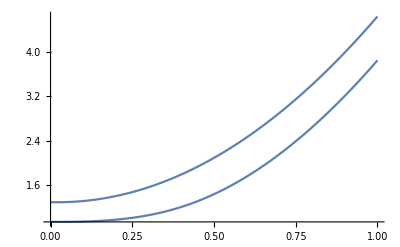

```mathematica
Plot[{l1[t], l2[t]}/.First@solinv, {t,0,1}]
```

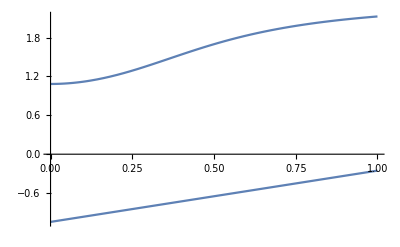

```mathematica
Plot[{ϕ1[t], α[t]}/.First@solinv, {t,0,1}]
```

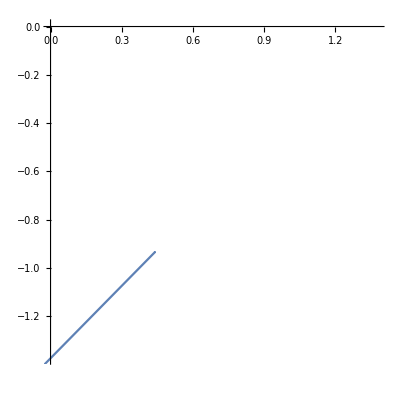

```mathematica
ParametricPlot[r/.First@solinv, {t,0,1},PlotRange->{{0,W},{-H,0}} ]
```

```mathematica
animObj = BotAnimation[solinv, {0,1}];
```

```mathematica
ListAnimate[animObj["FrameList"]]
```